# Vorbereitung 31

```mathematica
ClearAll["Global`*"]
```

## Konstanten

```mathematica
a=3.658*10^(6)*10^5*(10^(-2))^6
```

0.3658

```mathematica
b=42.75*(10^(-2))^3
```

0.00004275

```mathematica
R=8.314;
```

```mathematica
ν=1;
```

## Plotting

```mathematica
Tc=8/27 a/(R b)
```

304.947

```mathematica
Vc=3 b ν
```

0.00012825

```mathematica
Pc=1/27 a/b^2
```

7.41323×10^6

```mathematica
Tvals=Sort[Join[DeleteCases[Range[265,500,20],305],{Tc}]]
```

{265,285,304.947,325,345,365,385,405,425,445,465,485}

```mathematica
Remove[
```

```mathematica
ColorData["TemperatureMap"]/@Rescale[Tvals]
```

{RGBColor[0.178927, 0.305394, 0.933501],RGBColor[0.321888909090909, 0.45322572727272714, 0.9417314545454546],RGBColor[0.48713838770446416, 0.5945199143295874, 0.9527684648082576],RGBColor[0.6908021818181818, 0.7583791818181818, 0.9698163636363636],RGBColor[0.8620621818181817, 0.8928489999999999, 0.9867054545454546],RGBColor[0.9577412727272726, 0.9680040909090908, 0.956417181818182],RGBColor[0.9902410909090908, 0.9902324545454546, 0.8113939090909092],RGBColor[0.9935135454545455, 0.9885344545454546, 0.5353676363636367],RGBColor[0.9659284545454546, 0.8967308181818184, 0.32213890909090936],RGBColor[0.9136335454545457, 0.695292818181819, 0.24936572727272743],RGBColor[0.8625706363636365, 0.46884718181818263, 0.20703790909090924],RGBColor[0.817319, 0.134127, 0.164218]}

```mathematica
Show[Plot[Evaluate[Table[(ν R T)/(V-ν b)-(ν^2 a)/V^2,{T,Tvals}]],{V,0,0.0004},Frame->True,Axes->False,PlotRange->{Automatic,{0,1.5 10^7}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],PlotStyle->ColorData["ThermometerColors"]/@Rescale[Tvals],PlotLegends->BarLegend[{ColorData["ThermometerColors"],{Min[Tvals],Max[Tvals]}},LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}]],Graphics[{Point[{Vc,Pc}]}]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"figA1.pdf",Show[Plot[Evaluate[Table[(ν R T)/(V-ν b)-(ν^2 a)/V^2,{T,Tvals}]],{V,0,0.0004},Frame->True,Axes->False,PlotRange->{Automatic,{0,1.5 10^7}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],PlotStyle->ColorData["ThermometerColors"]/@Rescale[Tvals],PlotLegends->BarLegend[{ColorData["ThermometerColors"],{Min[Tvals],Max[Tvals]}},LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}]],Graphics[{Point[{Vc,Pc}]}]],Background->None];
```

## Maxwellsche Gerade

```mathematica
T0=288.7;
```

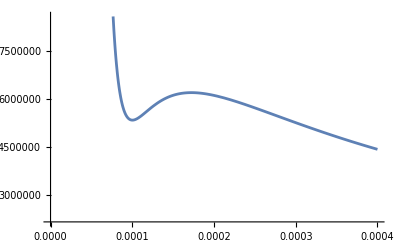

```mathematica
Plot[(ν R T0)/(V-ν b)-(ν^2 a)/V^2,{V,0,0.0004}]
```

```mathematica
Sort@Flatten@Values@Solve[(ν R T0)/(V-ν b)-(ν^2 a)/V^2==6*10^6, V]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.0000862918,0.000138634,0.000217867}

```mathematica
intersectionPoints[Pval_]:=Sort[Flatten[Values[Solve[(ν R T0)/(V-ν b)-(ν^2 a)/V^2==Pval,V]]]]
```

```mathematica
Integrate[(ν R T0)/(V-ν b)-(ν^2 a)/V^2-6*10^6,{V,0.00008629176831216918,0.00021786655673822965}]
```

-9.04073

```mathematica
area[Pval2_]:=With[{vals =intersectionPoints[Pval2]},Integrate[(ν R T0)/(V-ν b)-(ν^2 a)/V^2-Pval2,{V,vals[[1]],vals[[3]]}]]
```

```mathematica
min=5.3*10^6;
max=6.2*10^6;
```

```mathematica
toler=1
```

1

```mathematica
While[Abs[max-min]>toler, mid=(max+min)/2; If[area[mid]<0,max=mid, min=mid];Print[{max,min,mid}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{6.2×10^6,5.75×10^6,5.75×10^6}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{5.975×10^6,5.75×10^6,5.975×10^6}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{5.975×10^6,5.8625×10^6,5.8625×10^6}

{5.975×10^6,5.91875×10^6,5.91875×10^6}

{5.94688×10^6,5.91875×10^6,5.94688×10^6}

{5.94688×10^6,5.93281×10^6,5.93281×10^6}

{5.93984×10^6,5.93281×10^6,5.93984×10^6}

{5.93633×10^6,5.93281×10^6,5.93633×10^6}

{5.93457×10^6,5.93281×10^6,5.93457×10^6}

{5.93369×10^6,5.93281×10^6,5.93369×10^6}

{5.93369×10^6,5.93325×10^6,5.93325×10^6}

{5.93347×10^6,5.93325×10^6,5.93347×10^6}

{5.93336×10^6,5.93325×10^6,5.93336×10^6}

{5.93336×10^6,5.93331×10^6,5.93331×10^6}

{5.93336×10^6,5.93333×10^6,5.93333×10^6}

{5.93335×10^6,5.93333×10^6,5.93335×10^6}

{5.93334×10^6,5.93333×10^6,5.93334×10^6}

{5.93334×10^6,5.93333×10^6,5.93334×10^6}

{5.93334×10^6,5.93333×10^6,5.93334×10^6}

«1 more identical outputs»

```mathematica
intersections=intersectionPoints[mid];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
func[x_]:=Piecewise[{{mid,intersections[[1]]<x<intersections[[-1]]} }]
```

```mathematica
func2[x_]:=ConditionalExpression[mid, intersections[[1]]<x<intersections[[-1]]]
```

```mathematica
Plot[{(ν R T0)/(V-ν b)-(ν^2 a)/V^2},{V,0,0.0004},PlotRange->Automatic]
```

-Graphics-

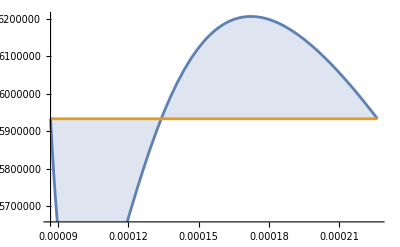

```mathematica
Plot[{(ν R T0)/(V-ν b)-(ν^2 a)/V^2, mid},{V, intersections[[1]], intersections[[3]]},Filling->{1->{2}},PlotRange->Automatic]
```

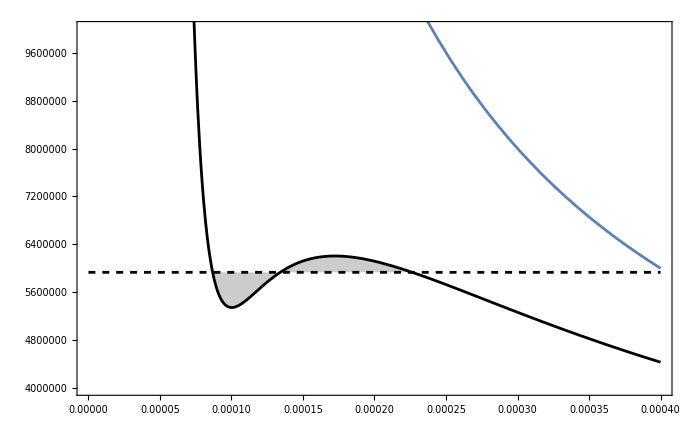

```mathematica
Show[Plot[{(ν R T0)/(V-ν b)-(ν^2 a)/V^2, mid,(ν R T0)/V},{V,0,0.0004},PlotRange->Automatic,PlotStyle->{Black,Directive[Black,Dashed],ColorData[97,1]}],Plot[{(ν R T0)/(V-ν b)-(ν^2 a)/V^2, mid},{V, intersections[[1]], intersections[[3]]},Filling->{1->{2}},PlotRange->All,PlotStyle->Transparent],Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],PlotRange->{All,{4*10^6,1*10^7}}]
```

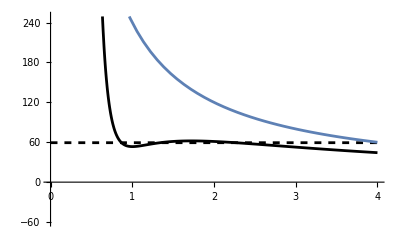

```mathematica
Plot[{10^(-5)((ν R T0)/((V/10^4)-ν b)-(ν^2 a)/((V/10^4)^2)),10^(-5) mid,10^(-5)(ν R T0)/(V/10^4)},{V,0,4},PlotRange->Automatic,PlotStyle->{Black,Directive[Black,Dashed],ColorData[97,1]}]
```

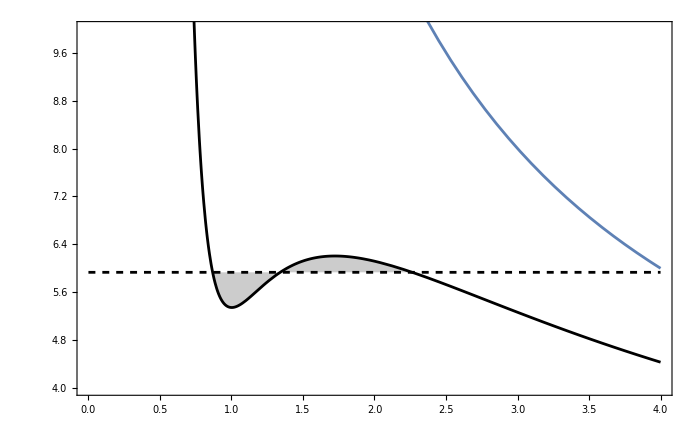

```mathematica
Show[Plot[{10^(-6)((ν R T0)/((V/10^4)-ν b)-(ν^2 a)/((V/10^4)^2)),10^(-6) mid,10^(-6)(ν R T0)/(V/10^4)},{V,0,4},PlotRange->Automatic,PlotStyle->{Black,Directive[Black,Dashed],ColorData[97,1]}],Plot[{10^(-6)((ν R T0)/((V/10^4)-ν b)-(ν^2 a)/((V/10^4)^2)),10^(-6) mid},{V,10^4 intersections[[1]], 10^4intersections[[3]]},Filling->{1->{2}},PlotRange->All,PlotStyle->Transparent],Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],PlotRange->{All,{4,10}}]
```

```mathematica
Export[NotebookDirectory[]<>"figA2.pdf",Show[Plot[{10^(-6)((ν R T0)/((V/10^4)-ν b)-(ν^2 a)/((V/10^4)^2)),10^(-6) mid,10^(-6)(ν R T0)/(V/10^4)},{V,0,4},PlotRange->Automatic,PlotStyle->{Black,Directive[Black,Dashed],ColorData[97,1]}],Plot[{10^(-6)((ν R T0)/((V/10^4)-ν b)-(ν^2 a)/((V/10^4)^2)),10^(-6) mid},{V,10^4 intersections[[1]], 10^4intersections[[3]]},Filling->{1->{2}},PlotRange->All,PlotStyle->Transparent],Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],PlotRange->{All,{4,10}}],Background->None];
```

```mathematica
mid
```

5.93334×10^6

```mathematica
max
```

5.93334×10^6

```mathematica
mid
```

5.93334×10^6